```mathematica
SetDirectory[NotebookDirectory[]];
<<SGT`
```

```mathematica
data=Simulate[
InitialPopulation->Randomized[{-1,0,1},"Smoothing"->1],
Payoff->RockPaperScissors,AgentType->"Constant",
Size->50,Steps->1;;100]
```

SimulationData[<100/100>]

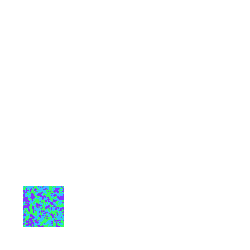
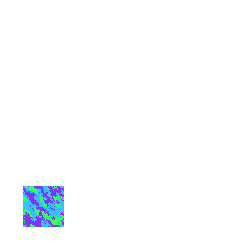
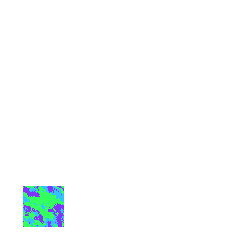
-Graphics-t = 1 | -Graphics-t = 50 | -Graphics-t = 100

```mathematica
Visualize[data,Panels->3,Show->"Agents",ColorFunction-> PastelHue,Alignment->Vertical]
```